## Background

```mathematica
rawMetadata=Import["/Users/katjad/Documents/Github/SheepCapstone/Salt6_corners_food locations_collective decision making_March2019.csv"];
```

```mathematica
paddock=rawMetadata[[-4;;-1,-2;;-1]];
feeding=rawMetadata[[2;;11,-2;;-1]];
water=rawMetadata[[12,-2;;-1]];
```

```mathematica
paddockRegion=BoundaryDiscretizeGraphics[Polygon[paddock]];metadataGraphic=Graphics[{LightBrown,Polygon[paddock],Darker[Green],Circle[#,30]&/@feeding,Thick,Darker[Blue],Circle[water,50]}];
```

```mathematica
rawXs=Import["/Users/katjad/Documents/Github/SheepCapstone/xs.csv"];
rawYs=Import["/Users/katjad/Documents/Github/SheepCapstone/ys.csv"];
rawIDs=Import["/Users/katjad/Documents/Github/SheepCapstone/ids.csv","Numeric"->False];
rawTs=Import["/Users/katjad/Documents/Github/SheepCapstone/ts.csv"];
rawTsStart=Import["/Users/katjad/Documents/Github/SheepCapstone/period.start.idxs.csv"];
```

```mathematica
Dimensions[rawXs]
```

{52,210352}

```mathematica
rawCoordinates=Table[{rawXs[[x,y]],rawYs[[x,y]]},{x,2,52},{y,2,210352}]/."NA"->Missing[];
```

## Sheep Personality Data

Match each rawID with it’s index

```mathematica
indexToEartag=AssociationThread[Range[51],rawIDs[[2;;,2]]];
```

```mathematica
indexToEartag
```

```mathematica
eartagsToFID=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/IDmatching/eartagsToFID.mx"];
```

```mathematica
indexToFID=indexToEartag/.eartagsToFID
```

<|1→NA,2→{14.55,15.96,12.47,22.36},3→{6.07,13.63,12.26,14.15},4→{15.57,12.86,15.17},5→{4.64,10.91,6.74,10.6},6→{2.63,6.38,7.33,5.86},7→{13.62,11.96,9.39,12.94},8→NA,9→{9.49,13.29,9.94,11.2},10→NA,11→{6.35,5.41,2.43,1.74},12→{15.84,14.84,12.74,22.6},13→{14.68,12.08,12.68,14.56},14→NA,15→{16.2,16.41,16.01,6.09},16→{9.41,21.52,12.85,13.8},17→{13.6,13.6,10.74,12.05},18→NA,19→{21.78,15.1,13.7,16.3},20→{7.28,12.56,7.3,6.75},21→NA,22→{14.13,10.7,14.42,16.22},23→{7.92,14.98,12.79,11.8},24→NA,25→{12.2,11.41,5.48,7.05},26→{13.55,14.03,14.1,15.1},27→{10.34,13.3,10.08,11.9},28→{5.11,10.65,8.48,2.17},29→{15.34,15.51,14.14,23.25},30→{5.1,6.44,2.84,0.25},31→NA,32→{11.15,6.75,7.91,14.46},33→{7.48,12.39,4.5,2.82},34→{4.3,3.13,1.9,3.95},35→{5.48,3.9,2.84,7.28},36→{2.11,14.3,7.68,12.4},37→{10.9,4.9,5.41,8.79},38→{14.29,22.18,14.52,22.22},39→{4.94,6,5.8,5.5},40→{9.07,5.9,8.57,4.7},41→{7.78,9.29,3.84,11.1},42→{6.96,5.98,8.87,13.65},43→NA,44→{7.39,9.28,3.62,10.56},45→{5.96,4.67,11.07,22.2},46→NA,47→NA,48→{9.27,6.2,9.78,5.89},49→{12.1,13.72,12.88,14.07},50→{6.8,5.42,2.62,3.15,3.03},51→NA|>

```mathematica
indexToMeanFID = MapAt[Mean,indexToFID,All]/.Mean["NA"]->"NA"
```

<|1→NA,2→16.335,3→11.5275,4→14.5333,5→8.2225,6→5.55,7→11.9775,8→NA,9→10.98,10→NA,11→3.9825,12→16.505,13→13.5,14→NA,15→13.6775,16→14.395,17→12.4975,18→NA,19→16.72,20→8.4725,21→NA,22→13.8675,23→11.8725,24→NA,25→9.035,26→14.195,27→11.405,28→6.6025,29→17.06,30→3.6575,31→NA,32→10.0675,33→6.7975,34→3.32,35→4.875,36→9.1225,37→7.5,38→18.3025,39→5.56,40→7.06,41→8.0025,42→8.865,43→NA,44→7.7125,45→10.975,46→NA,47→NA,48→7.785,49→13.1925,50→4.204,51→NA|>

```mathematica
range=MinMax[DeleteCases[Values[indexToFID],"NA"]]
```

{0.25,23.25}

### Basic Visualization

```mathematica
CoolColor[ z_ ] :=RGBColor[z,1-z,1]
```

```mathematica
CoolColor[1]
```

RGBColor[1, 0, 1]

```mathematica
personalityVisual=Animate[Show[
metadataGraphic,
Graphics[
MapThread[
If[MemberQ[#1,Missing[]],
Nothing,
Style[{Thick,Circle[#1,15]},
If[#2==="NA",Black,CoolColor[Rescale[#2,range,{0,1}]]]]]&,{rawCoordinates[[All,n]],Values[indexToMeanFID]}]],PlotRange->{{580401.,585573.},{6.562693*^6,6.564282*^6}}],{n,100,10000,25}];
```

```mathematica
Export["personalitySampleMotion.gif",personalityVisual,"DisplayDurations"->0.1]
```

personalitySampleMotion.gif

51

### Average Sheep personality per group

```mathematica
dbScanHerds50=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds50.mx"];
```

```mathematica
dbScanHerds50[[100]]
```

{{2,3,4,5,7,8,9,10,11,12,14,16,17,18,20,21,22,23,24,25,26,29,31,33,34,35,36,37,38,39,40,41,42,44,45,46,47,48,51},{}}

```mathematica
personalityHerds=dbScanHerds50/.indexToMeanFID/."NA"->Missing[];
```

```mathematica
personalityHerds//Length
```

210351

```mathematica
personalityHerds[[500]]
```

{{Missing[],16.335,11.5275,14.5333,8.2225,5.55,11.9775,Missing[],10.98,Missing[],3.9825,16.505,13.5,13.6775,12.4975,8.4725,Missing[],13.8675,11.8725,14.195,6.6025,17.06,3.6575,Missing[],10.0675,6.7975,4.875,9.1225,18.3025,7.06,8.0025,7.7125,10.975,Missing[],7.785},{Missing[],14.395,Missing[],Missing[]},{Missing[],Missing[],9.035,3.32,7.5,5.56,8.865},{}}

```mathematica
averagePersonality=Mean/@DeleteCases[DeleteCases[Catenate[personalityHerds[[All,1;;-2]]],Missing[],2],{}];
```

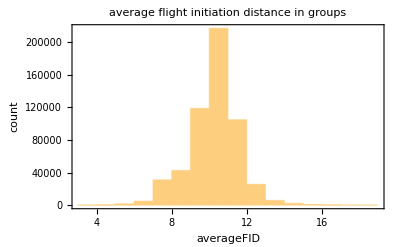

```mathematica
Histogram[averagePersonality,{1},Frame->True,FrameLabel->{"averageFID","count"},PlotLabel->"average flight initiation distance in groups"]
```

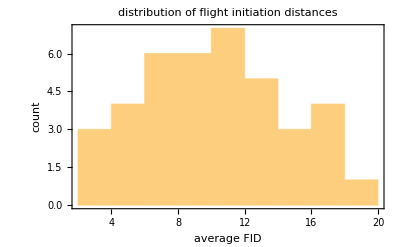

```mathematica
Histogram[DeleteCases[Values[indexToMeanFID],"NA"],{2},Frame->True,FrameLabel->{"average FID","count"},PlotLabel->"distribution of flight initiation distances"]
```

### Sheep personality and time spent alone

```mathematica
ResourceFunction["RegressionListPlot"]
```

```mathematica
groupStability50=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/GroupStability/groupStability50.mx"];
```

Import data on how long each sheep spent by itself.

```mathematica
groupStability50
```

<|{5,8,17,21,22,33,35,38,40,44,48}→{1},{2,3,4,5,7,8,9,10,11,12,14,16,17,18,19,20,21,22,23,24,25,26,27,29,31,33,34,35,36,37,38,39,40,41,42,44,45,46,47,48,51}→{2},11034,{12,44,50}→{210351},{31,46}→{210351}|>
 |  |  |  |

```mathematica
groupToTimeAlone
```

<|{1}→0,{2}→0,{3}→0,{4}→0,{5}→0,{6}→0,{7}→0,{8}→0,{9}→0,{10}→0,{11}→0,{12}→0,{13}→0,{14}→0,{15}→0,{16}→0,{17}→0,{18}→0,{19}→0,{20}→0,{21}→0,{22}→0,{23}→0,{24}→0,{25}→0,{26}→0,{27}→0,{28}→0,{29}→0,{30}→0,{31}→0,{32}→0,{33}→0,{34}→0,{35}→0,{36}→0,{37}→0,{38}→0,{39}→0,{40}→0,{41}→0,{42}→0,{43}→0,{44}→0,{45}→0,{46}→0,{47}→0,{48}→0,{49}→0,{50}→0,{51}→0|>

```mathematica
groupToTimeAlone=Length/@KeySelect[SortBy[groupStability50,Length],Length[#]==1&][[;;51]];
```

```mathematica
indexToTimeAlone=Association[#->groupToTimeAlone[{#}]&/@Range[51]]
```

<|1→16767,2→36868,3→15594,4→3852,5→12785,6→15385,7→15503,8→7196,9→11552,10→11849,11→20256,12→9656,13→16911,14→8966,15→10357,16→22185,17→8923,18→9965,19→2667,20→15945,21→5707,22→23039,23→21234,24→6885,25→9428,26→13631,27→18062,28→8871,29→10636,30→14145,31→18373,32→8791,33→14488,34→11568,35→11531,36→15145,37→10979,38→14739,39→15422,40→13653,41→6126,42→14077,43→16729,44→10808,45→15161,46→28529,47→10856,48→6924,49→12171,50→2963,51→4138|>

```mathematica
FIDTimeAlone=DeleteCases[Table[{indexToMeanFID[x],indexToTimeAlone[x]},{x,51}],{"NA",_}]
```

{{16.335,36868},{11.5275,15594},{14.5333,3852},{8.2225,12785},{5.55,15385},{11.9775,15503},{10.98,11552},{3.9825,20256},{16.505,9656},{13.5,16911},{13.6775,10357},{14.395,22185},{12.4975,8923},{16.72,2667},{8.4725,15945},{13.8675,23039},{11.8725,21234},{9.035,9428},{14.195,13631},{11.405,18062},{6.6025,8871},{17.06,10636},{3.6575,14145},{10.0675,8791},{6.7975,14488},{3.32,11568},{4.875,11531},{9.1225,15145},{7.5,10979},{18.3025,14739},{5.56,15422},{7.06,13653},{8.0025,6126},{8.865,14077},{7.7125,10808},{10.975,15161},{7.785,6924},{13.1925,12171},{4.204,2963}}

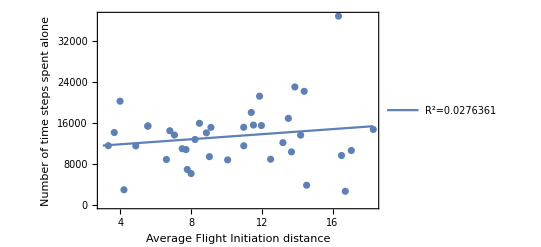

```mathematica
ResourceFunction["RegressionListPlot"][FIDTimeAlone,Frame->True,FrameLabel->{Style["Average Flight Initiation distance",Medium],Style["Number of time steps spent alone",Medium]},"DisplayRSquared"->True]
```

### Sheep Personality and average group size

```mathematica
dbScanHerds50 = Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds50.mx"];
```

```mathematica
dbScanHerds50LonelySheep=Join[Most[#],List/@Last[#]]&/@dbScanHerds50;
```

```mathematica
dbScanHerds50LonelySheep[[2000]]
```

{{2,4,5,8,11,13,16,17,19,23,25,26,34,39,41,42,44,45},{3,6,10,15,20,22,27,28,29,31,35,36,46},{7,9,21,32,38,48,49},{12,14,18,24,33,37,43,47,51},{1},{40}}

```mathematica
Catenate[Function[g,Function[s,s->Length[g]]/@g]/@dbScanHerds50LonelySheep[[2000]]]
```

{2→18,4→18,5→18,8→18,11→18,13→18,16→18,17→18,19→18,23→18,25→18,26→18,34→18,39→18,41→18,42→18,44→18,45→18,3→13,6→13,10→13,15→13,20→13,22→13,27→13,28→13,29→13,31→13,35→13,36→13,46→13,7→7,9→7,21→7,32→7,38→7,48→7,49→7,12→9,14→9,18→9,24→9,33→9,37→9,43→9,47→9,51→9,1→1,40→1}

```mathematica
Merge[Function[ts,Catenate[Function[g,Function[s,s->Length[g]]/@g]/@ts]]/@dbScanHerds50LonelySheep,Identity];
```

```mathematica
indexToGroupLengths50=%100;
```

```mathematica
Export["/Users/katjad/Documents/Github/SheepCapstone/MXs/GroupStability/indexToGroupLengths50.mx",indexToGroupLengths50]
```

/Users/katjad/Documents/Github/SheepCapstone/MXs/GroupStability/indexToGroupLengths50.mx

```mathematica
indexToMeanGroupLength50 = MapAt[Mean,indexToGroupLengths50,All];
```

```mathematica
indexToMeanGroupLength50//N
```

<|5→26.0722,8→25.0883,17→25.9763,21→25.7306,22→22.6279,33→24.6007,35→24.8867,38→22.9849,40→23.9745,44→25.152,48→26.7124,2→20.2187,3→24.0251,4→26.7068,7→23.614,9→24.3092,10→23.7885,11→23.2196,12→24.5263,14→26.3153,16→22.957,18→25.1892,19→26.9037,20→22.9761,23→11.0724,24→23.9396,25→23.9337,26→23.606,27→23.9538,29→24.8563,31→24.9627,34→25.5872,36→24.4537,37→23.0069,39→23.5859,41→26.1648,42→25.2367,45→25.115,46→22.1838,47→24.4033,51→25.9576,43→23.7656,32→25.1075,49→25.4796,28→25.1919,6→24.025,1→24.4494,30→23.9794,15→25.1275,13→23.9176,50→28.9448|>

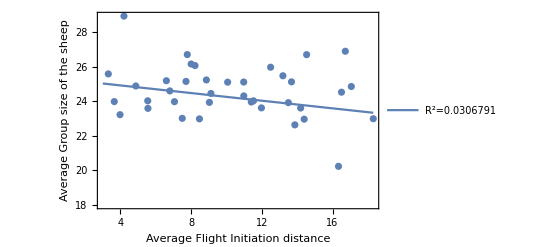

```mathematica
ResourceFunction["RegressionListPlot"][DeleteCases[Table[{indexToMeanFID[x],indexToMeanGroupLength50[x]//N},{x,51}],{"NA",_}],Frame->True,FrameLabel->{Style["Average Flight Initiation distance",Medium],Style["Average Group size of the sheep",Medium]},"DisplayRSquared"->True]
```

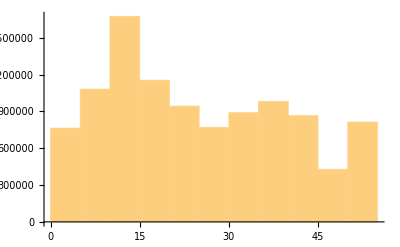

```mathematica
Histogram[Catenate[Values[indexToGroupLengths50]],{5}]
```

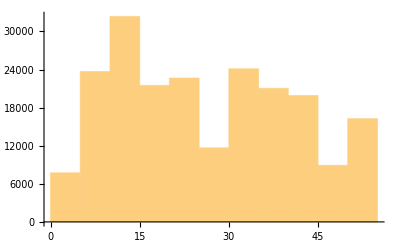

```mathematica
Histogram[indexToGroupLengths50[[4]],{5}]
```

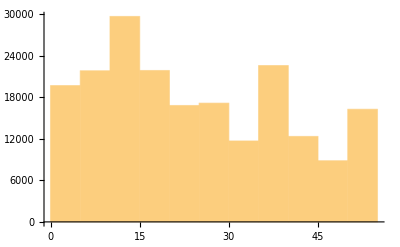

{{16.335,20.2187},{11.5275,24.0251},{14.5333,26.7068},{8.2225,26.0722},{5.55,24.025},{11.9775,23.614},{10.98,24.3092},{3.9825,23.2196},{16.505,24.5263},{13.5,23.9176},{13.6775,25.1275},{14.395,22.957},{12.4975,25.9763},{16.72,26.9037},{8.4725,22.9761},{13.8675,22.6279},{11.8725,11.0724},{9.035,23.9337},{14.195,23.606},{11.405,23.9538},{6.6025,25.1919},{17.06,24.8563},{3.6575,23.9794},{10.0675,25.1075},{6.7975,24.6007},{3.32,25.5872},{4.875,24.8867},{9.1225,24.4537},{7.5,23.0069},{18.3025,22.9849},{5.56,23.5859},{7.06,23.9745},{8.0025,26.1648},{8.865,25.2367},{7.7125,25.152},{10.975,25.115},{7.785,26.7124},{13.1925,25.4796},{4.204,28.9448}}

```mathematica
Histogram[indexToGroupLengths50[[50]],{5}]
```

## Group Stability and FID

```mathematica
groupStability50=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/GroupStability/groupStability50.mx"];
```

```mathematica
groupStability50
```

<|{5,8,17,21,22,33,35,38,40,44,48}→{1},{2,3,4,5,7,8,9,10,11,12,14,16,17,18,19,20,21,22,23,24,25,26,27,29,31,33,34,35,36,37,38,39,40,41,42,44,45,46,47,48,51}→{2},11034,{12,44,50}→{210351},{31,46}→{210351}|>
 |  |  |  |

```mathematica
({1,3,4}+1)*6
```

{12,24,30}

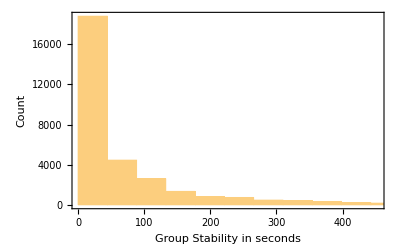

```mathematica
Histogram[(Values[groupStability50]+1)*6,Frame->True,FrameLabel->{"Group Stability in seconds","Count"}]
```

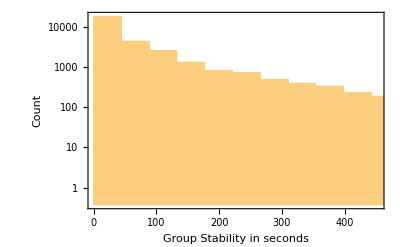

```mathematica
Histogram[(Values[groupStability50]+1)*6,ScalingFunctions->"Log",Frame->True,FrameLabel->{"Group Stability in seconds","Count"}]
```

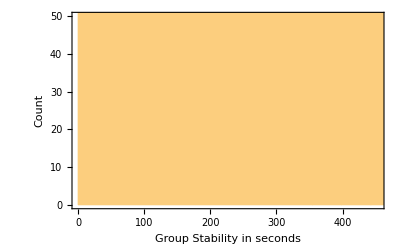

```mathematica
Histogram[(Values[groupStability50]+1)*6,PlotRange->{0,50},Frame->True,FrameLabel->{"Group Stability in seconds","Count"}]
```

```mathematica
meanFIDToStability=DeleteCases[KeyValueMap[{Mean[DeleteCases[#1/.indexToMeanFID,"NA"]],(#2+1)*6}&,Association[groupStability50]],{Mean[{}],_}];
```

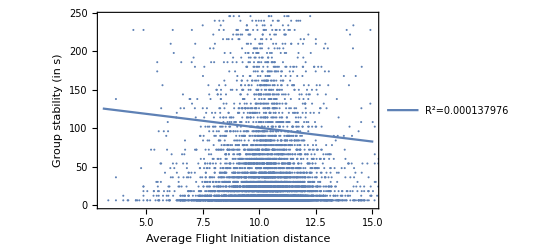

```mathematica
ResourceFunction["RegressionListPlot"][meanFIDToStability,Frame->True,FrameLabel->{Style["Average Flight Initiation distance",Medium],Style["Group stability (in s)",Medium]},"DisplayRSquared"->True]
```

```mathematica
SizeToStability=DeleteCases[KeyValueMap[{Length[#1],(#2+1)*6}&,Association[groupStability50]],{Mean[{}],_}]
```

{{1,6},{38,18},{12,6},{13,186},{9,6},{5,516},{1,6},{1,6},{1,6},{44,6},{18,108},{32,30},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},6845,{15,6},{11,6},{13,6},{15,6},{10,6},{12,6},{13,6},{14,6},{16,6},{11,6},{8,6},{7,6},{4,6},{8,6},{6,6},{2,6},{20,6},{2,6},{4,6},{35,6},{10,6},{14,6},{9,6}}
 |  |  |  |

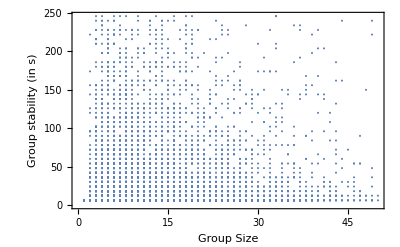

```mathematica
ListPlot[SizeToStability,Frame->True,FrameLabel->{Style["Group Size",Medium],Style["Group stability (in s)",Medium]}]
```

## Binned by group size

```mathematica
binnedFIDHerds=GroupBy[DeleteCases[Catenate[personalityHerds],{___Missing}],(Floor[Length[#],1]&)->(Mean[DeleteMissing[#]]&)];
```

{1}
 |  |  |  |

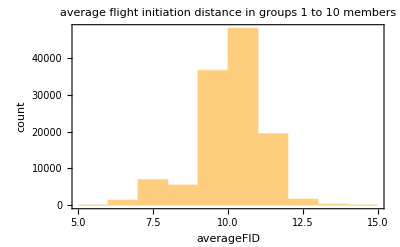

```mathematica
g1=Histogram[Catenate[Join[binnedFIDHerds[[#]]&/@Range[1,10]]],{1},Frame->True,FrameLabel->{"averageFID","count"},PlotLabel->"average flight initiation distance in groups 1 to 10 members"]
```

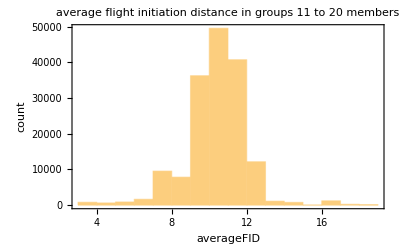

```mathematica
g2=Histogram[Catenate[Join[binnedFIDHerds[[#]]&/@Range[11,20]]],{1},Frame->True,FrameLabel->{"averageFID","count"},PlotLabel->"average flight initiation distance in groups 11 to 20 members"]
```

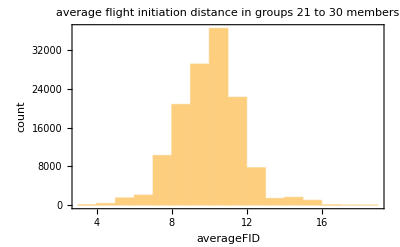

```mathematica
g3=Histogram[Catenate[Join[binnedFIDHerds[[#]]&/@Range[21,30]]],{1},Frame->True,FrameLabel->{"averageFID","count"},PlotLabel->"average flight initiation distance in groups 21 to 30 members"]
```

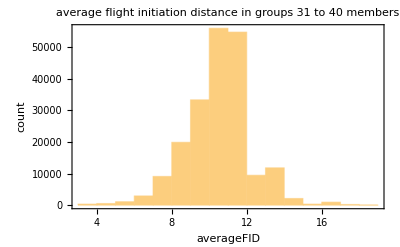

```mathematica
g4=Histogram[Catenate[Join[binnedFIDHerds[[#]]&/@Range[31,40]]],{1},Frame->True,FrameLabel->{"averageFID","count"},PlotLabel->"average flight initiation distance in groups 31 to 40 members"]
```

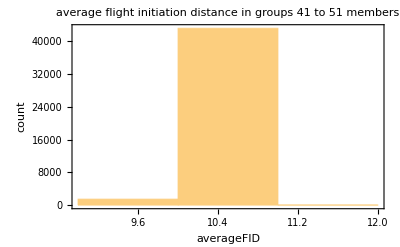

```mathematica
g5=Histogram[Catenate[Join[binnedFIDHerds[[#]]&/@Range[41,50]]],{1},Frame->True,FrameLabel->{"averageFID","count"},PlotLabel->"average flight initiation distance in groups 41 to 51 members"]
```

```mathematica
Grid[{{g1,g2},{g3,g4},{g5," "}}]
```

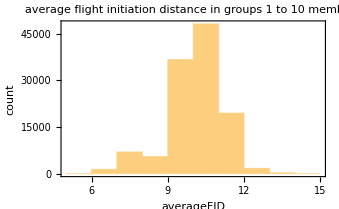
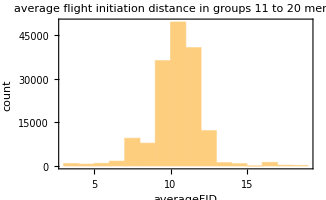
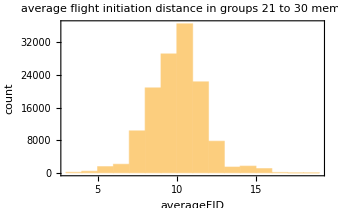
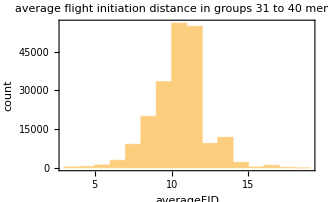
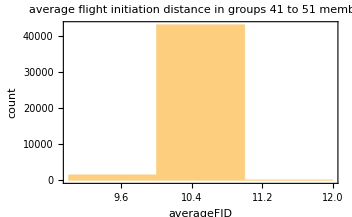
```mathematica
{{-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, " "}}
```

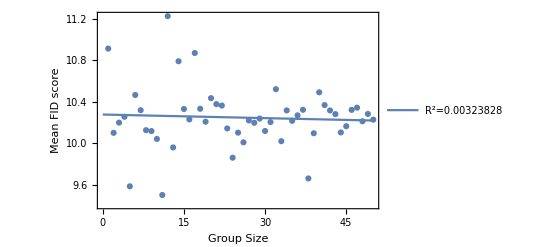

```mathematica
ResourceFunction["RegressionListPlot"][Map[#(*+{2.5,0}*)&,KeyValueMap[List,KeySort[Mean/@binnedFIDHerds]]],PlotRange->All,Frame->True,FrameLabel->{"Group Size","Mean FID score"},"DisplayRSquared"->True]
```